```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
i=0;
fileOBJ="xfab_flat"<>ToString[i]<>".obj"
filePDF ="cut"<>ToString[i]<>".pdf"
```

xfab_flat0.obj

cut0.pdf

```mathematica
input=Import[fileOBJ,"GraphicsComplex"];
v=Part[input,1];
f=Flatten[Cases[input,Triangle[x_]->x,Infinity],1];
```

```mathematica
AllEdges[f_]:=Flatten[Map[  {
   {Part[#,1],Part[#,2]},
   {Part[#,2],Part[#,3]},
   {Part[#,3],Part[#,1]},
   {Part[#,2],Part[#,1]},
   {Part[#,3],Part[#,2]},
  {Part[#,1],Part[#,3]}
  }&,f],1];
```

```mathematica
BoundaryLoop[f_]:=Module[{edgs,boundaryEdges,graph},
boundaryEdges=DirectedEdge@@@Part[Select[Tally[AllEdges[f]],Part[#,2]==1&],;;,1];
Part[FindHamiltonianCycle[boundaryEdges],1,;;,1]
];

InnerEdges[f]:=Part[Select[Tally[AllEdges[f]],Part[#,2]==2&],;;,1];
```

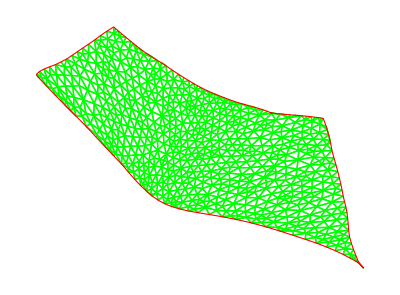

cut0.pdf

```mathematica
v2d=Part[v,;;,;;2];
loop=Part[v2d,BoundaryLoop[f]];
edges=InnerEdges[f];
gr=Graphics[{
FaceForm[],
Green,
Map[Line[Part[v2d,#]]&,edges],
EdgeForm[Red],
Polygon[loop]
}]
Export[filePDF,gr,"PDF"]
```

```mathematica
Norm[loop[[1]]]
```

4.93364